```mathematica
Step[list_]:=Flatten[Map[{(3#+1)/2,#/2}&,list]]
```

```mathematica
StepN[list_,n_]:=Block[{i,result=list},For[i=1,i≤n,i++,result=Step[result]];result]
```

```mathematica
Map[Factor,StepN[{x},3]]
```

{1/8 (19+27 x),1/8 (5+9 x),1/8 (7+9 x),1/8 (1+3 x),1/8 (10+9 x),1/8 (2+3 x),1/8 (4+3 x),x/8}

```mathematica
{x}//Step
```

{1/2 (1+3 x),x/2}

```mathematica
Map[Reduce [Assuming[x>1,#<=x]]&, {x}//Step//Step]
```

{x≤-1,x≥1,x≥2,x≥0}

```mathematica
Map[Simplify [Assuming[x>1&&Element[x,Integers],#<=x]]&, StepN[{x},3]]
```

{1+x≤0,5+x≤0,7+x≤0,5 x≥1,10+x≤0,5 x≥2,5 x≥4,x≥0}

```mathematica
Map[Reduce[Assuming[x>1&&Element[x,Integers],#<=x],x]&, StepN[{x},3]]//TableForm
```

x≤-1
x≤-5
x≤-7
x≥1/5
x≤-10
x≥2/5
x≥4/5
x≥0

```mathematica
Fold[And,Table[Indexed[x,i+1]==2*Indexed[x,i]+1,{i,10}]]
```

```mathematica
Table[Indexed[x,i]==2*Indexed[x,i+1]+1,{i,3}]
```

{x1==1+2 x2,x2==1+2 x3,x3==1+2 x4}

```mathematica
Reduce[Fold[And,Table[Indexed[x,i]==2*Indexed[x,i+1]+1,{i,5}]],Indexed[x,1]]
```

x5==1+2 x6&&x4==3+4 x6&&x3==7+8 x6&&x2==15+16 x6&&x1==31+32 x6

```mathematica
MarkovProcessProperties
```

```mathematica
"x goes to (3x+1)/2"
```

```mathematica
x->2Indexed[x,1]+1
```

x→1+2 x1

```mathematica
Simplify[(3x+1)/2/.x->1+2 x1]
```

2+3 x1

```mathematica
Step3[list_]:=Map[Simplify[(3#+1)/2]&,list]
```

```mathematica
Step3N[list_,n_]:=Block[{i,result=list},For[i=1,i≤n,i++,result=Step3[result]];result]
```

```mathematica
{2+3 x1}//Step3
```

{1/2 (7+9 x1)}

```mathematica
1/2 (7+9 x1)/.Indexed[x,1]->3
```

17

Dus is x1 oneven

```mathematica
Indexed[x,1]->2Indexed[x,2]+1
```

x1→1+2 x2

```mathematica
Simplify[(x->1+2 x1)/.x1->1+2 x2]
```

x→3+4 x2

```mathematica
Table[Simplify[Step3N[{x},step]/.x->3+4 x2],{step,5}]
```

{{5+6 x2},{8+9 x2},{1/2 (25+27 x2)},{1/4 (77+81 x2)},{1/8 (235+243 x2)}}

```mathematica
Step[list_]:=Flatten[Map[{(3#+1)/2,#/2}&,list]]
```

```mathematica
MySmaller[exp1_,exp2_]:=(Assuming[x>1,Reduce[exp1<exp2,x,Integers]]/.x->10000)
```

```mathematica
MySmaller[exp1_,exp2_]:=(exp1<exp2/.x->100000000)
```

```mathematica
MySmaller[x/2,x]
```

True

```mathematica
MySmaller[x,x/2]
```

False

```mathematica
StepTree[form_,n_]:=Block[{result={},current={form},next={},nextexp,i},
For[i=1,i≤n,i++,
Table[
nextexp=Simplify[(3 *exp+1)/2];
AppendTo[result,Labeled[exp->nextexp,Style["*3",Darker[Green],12,Bold]]];
If[MySmaller[form,nextexp],
AppendTo[next,nextexp]
];
nextexp=Simplify[(exp)/2];
AppendTo[result,Labeled[exp->nextexp,Style["/2",Red,12,Bold]]];
If[MySmaller[form,nextexp],
AppendTo[next,nextexp]
];
,{exp,current}
];
current=next;
next={}
];
result
]
```

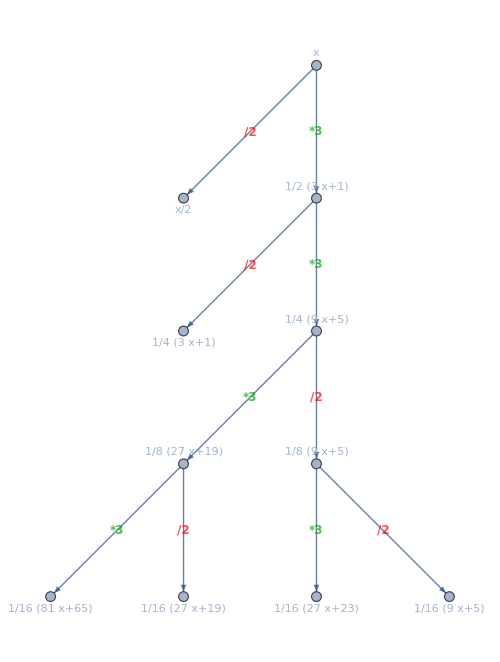

```mathematica
Graph[Simplify[StepTree[x,4]],VertexLabels->"Name", EdgeLabels->"Name",GraphLayout->"LayeredDigraphEmbedding", ImageSize->500]
```

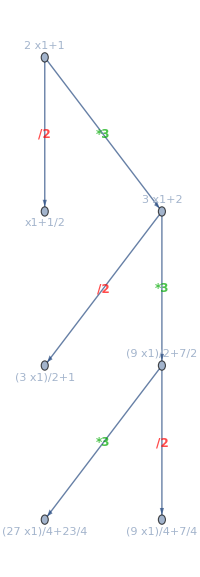

```mathematica
Graph[Simplify[StepTree[x,3]/.x->1+2 x1],VertexLabels->"Name", GraphLayout->"LayeredDigraphEmbedding", ImageSize->200]
```

```mathematica
IndexedX[i_]:=If[i==0,x,Indexed[x,i]]
```

```mathematica
Table[IndexedX[k],{k,0,3}]
```

{x,x1,x2,x3}

```mathematica
SwapN[form_,n_]:=Block[{result=form,i},
For[i=1,i≤n,i++,
result=result/.(IndexedX[i-1]->2*IndexedX[i]+1)
];
Simplify[result]
]
```

```mathematica
SwapN[x,3]
```

```mathematica
SwapNSlow[form_,n_]:=Block[{result=form,i},
For[i=1,i≤n,i++,
result={result,(IndexedX[i-1]->2*IndexedX[i]+1),result/.(IndexedX[i-1]->2*IndexedX[i]+1)}
];
Simplify[result]
]
```

```mathematica
TableForm[Table[{k,SwapN[x,k],SwapNSlow[x,k]},{k,0,3}],TableDepth->1]
```

{0,x,x}
{1,1+2 x1,{x,x→1+2 x1,1+2 x1}}
{2,3+4 x2,{{x,x→1+2 x1,1+2 x1},x1→1+2 x2,{x,x→3+4 x2,3+4 x2}}}
{3,7+8 x3,{{{x,x→1+2 x1,1+2 x1},x1→1+2 x2,{x,x→3+4 x2,3+4 x2}},x2→1+2 x3,{{x,x→1+2 x1,1+2 x1},x1→3+4 x3,{x,x→7+8 x3,7+8 x3}}}}

```mathematica
First[Solve[IndexedX[1]==2IndexedX[2]+1,IndexedX[1]]]
```

{x1→1+2 x2}

```mathematica
1+2 x1/.First[Solve[IndexedX[1]==2IndexedX[2]+1,IndexedX[1]]]//Simplify
```

3+4 x2

```mathematica
Assuming[x>2,Reduce[8x+7>2(8x+7),x,Integers]]/.x->1
```

False

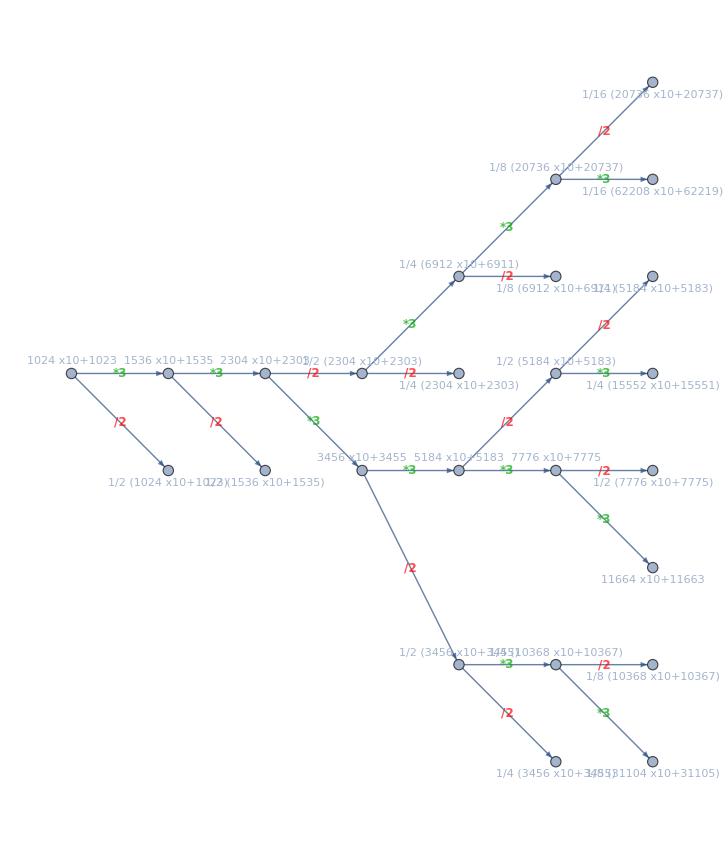

```mathematica
With[{g=StepTree[x,6]/.x->SwapN[x,10]},
Graph[g,VertexLabels->Map[#->FactorTerms[Simplify[#]]&,VertexList[g]],GraphLayout->{"LayeredDigraphEmbedding","Orientation"->Left}, ImageSize->600]
]
```

```mathematica
MySmaller[9x+17/2,8x+7]
```

False

```mathematica
MySmaller[8x+7,9x+17/2]
```

True

```mathematica
IntegerDigits[20737,2]
```

{1,0,1,0,0,0,1,0,0,0,0,0,0,0,1}

```mathematica
IntegerDigits[31105,2]
```

{1,1,1,1,0,0,1,1,0,0,0,0,0,0,1}

```mathematica
IntegerDigits[31104,2]
```

{1,1,1,1,0,0,1,1,0,0,0,0,0,0,0}

```mathematica
SwapN[x,10]
```

1023+1024 x10

```mathematica
Map[PadLeft[IntegerDigits[Last[#],2],10]&,Map[CoefficientList[#,IndexedX[10]]&,(StepN[ {x},6]//Simplify)/.x->SwapN[x,10]]]//Sort//MatrixPlot
```

-Graphics-

```mathematica
Table[3^i,{i,10}]
```

{3,9,27,81,243,729,2187,6561,19683,59049}

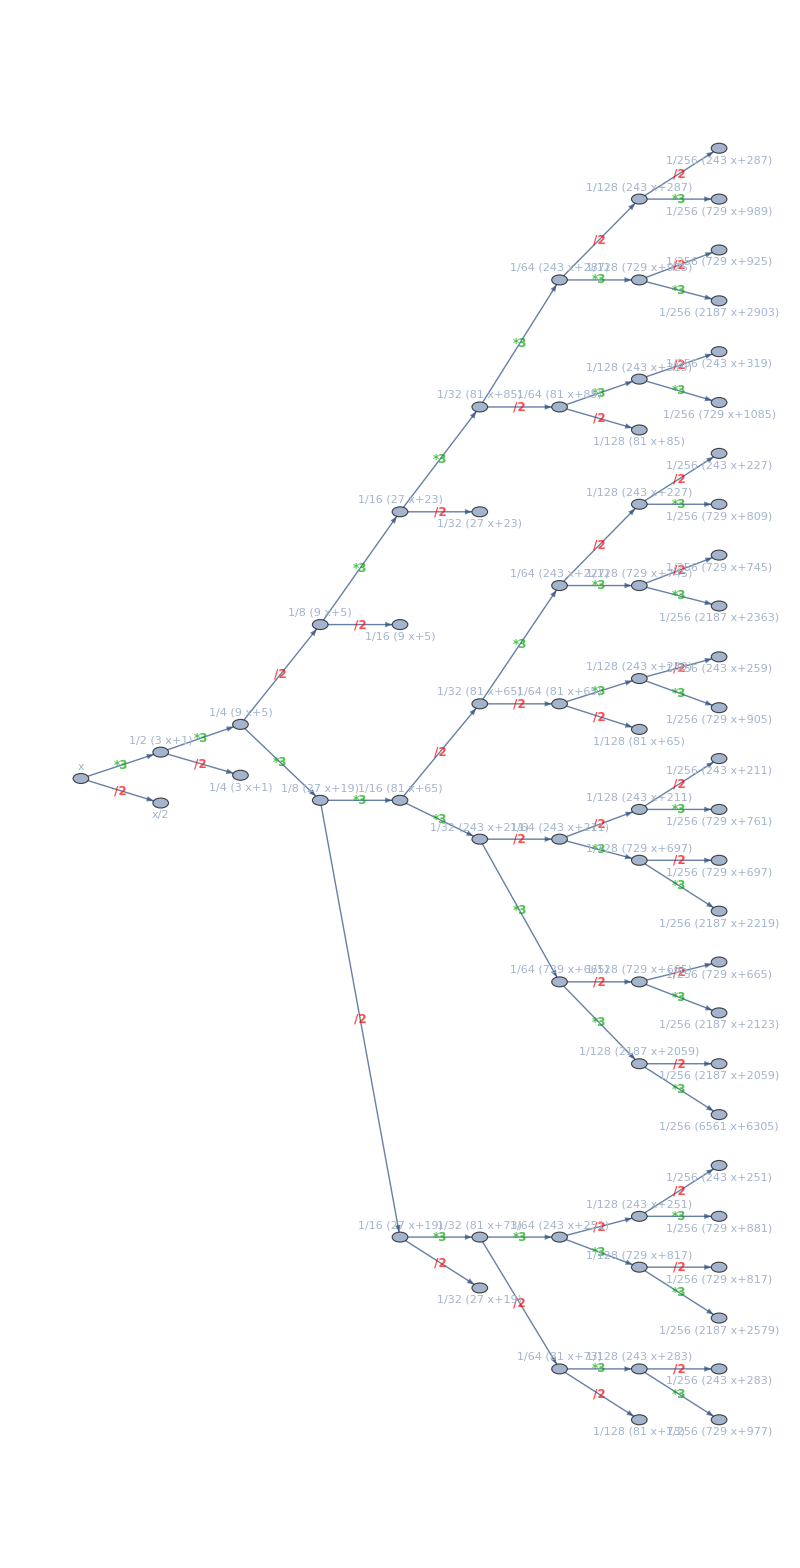

```mathematica
With[{g=StepTree[x,8]/.x->SwapN[x,0]},
Graph[g,VertexLabels->Map[#->FullSimplify[#]&,VertexList[g]],GraphLayout->{"LayeredDigraphEmbedding","Orientation"->Left}, ImageSize->800]
]
```

```mathematica
VertexList[StepTree[x,8]]
```

{x,1/2 (1+3 x),x/2,1/4 (5+9 x),1/4 (1+3 x),1/8 (19+27 x),1/8 (5+9 x),1/16 (65+81 x),1/16 (19+27 x),1/16 (23+27 x),1/16 (5+9 x),1/32 (211+243 x),1/32 (65+81 x),1/32 (73+81 x),1/32 (19+27 x),1/32 (85+81 x),1/32 (23+27 x),1/64 (665+729 x),1/64 (211+243 x),1/64 (227+243 x),1/64 (65+81 x),1/64 (251+243 x),1/64 (73+81 x),1/64 (287+243 x),1/64 (85+81 x),1/128 (2059+2187 x),1/128 (665+729 x),1/128 (697+729 x),1/128 (211+243 x),1/128 (745+729 x),1/128 (227+243 x),1/128 (259+243 x),1/128 (65+81 x),1/128 (817+729 x),1/128 (251+243 x),1/128 (283+243 x),1/128 (73+81 x),1/128 (925+729 x),1/128 (287+243 x),1/128 (319+243 x),1/128 (85+81 x),1/256 (6305+6561 x),1/256 (2059+2187 x),1/256 (2123+2187 x),1/256 (665+729 x),1/256 (2219+2187 x),1/256 (697+729 x),1/256 (761+729 x),1/256 (211+243 x),1/256 (2363+2187 x),1/256 (745+729 x),1/256 (809+729 x),1/256 (227+243 x),1/256 (905+729 x),1/256 (259+243 x),1/256 (2579+2187 x),1/256 (817+729 x),1/256 (881+729 x),1/256 (251+243 x),1/256 (977+729 x),1/256 (283+243 x),1/256 (2903+2187 x),1/256 (925+729 x),1/256 (989+729 x),1/256 (287+243 x),1/256 (1085+729 x),1/256 (319+243 x)}

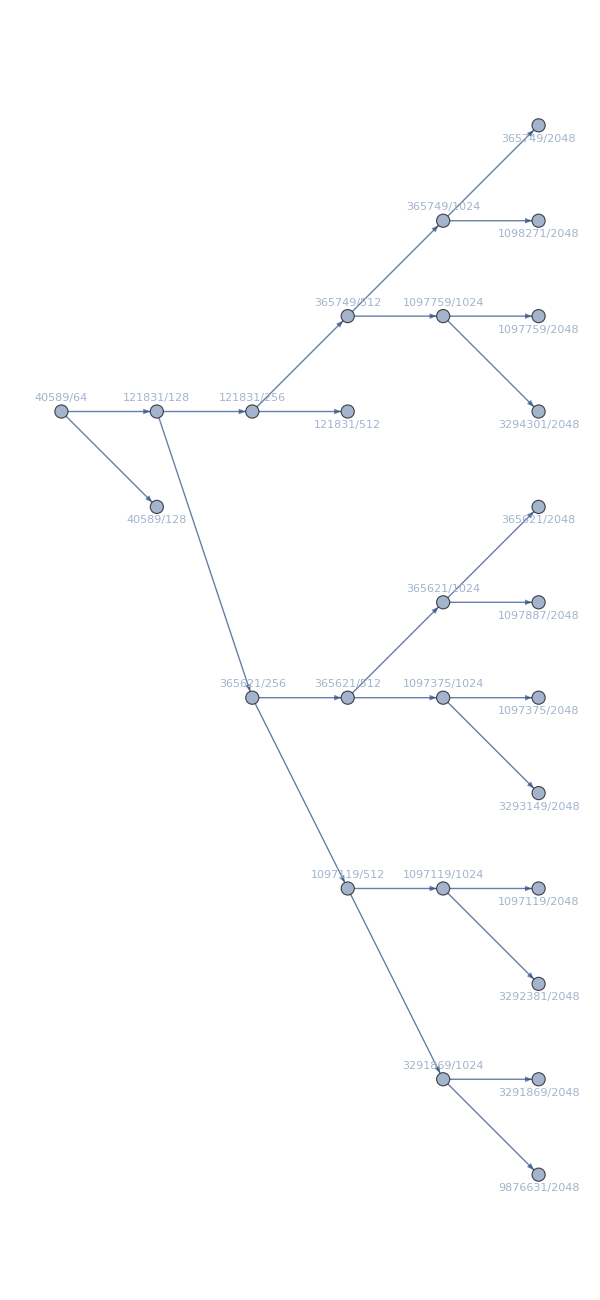

```mathematica
With[{h=StepTree[x,12]},
With[{g=EdgeList[Subgraph[h,VertexOutComponent[h,1/128 (259+243 x)]]]/.x->333},
Graph[g,VertexLabels->Map[#->FullSimplify[#]&,VertexList[g]],GraphLayout->{"LayeredDigraphEmbedding","Orientation"->Left}, ImageSize->600]
]
]
```